# Optical Trap for ground-state CO molecules

## Here we analyse and show various physical constraints involved in optical trapping of cold CO molecules. These molecules are subjected to a strong Stark deceleration when they are in the excited a^3 Π_1 state, and furthermore they can be transferred with high efficiency to their absolute ground-state X^1 Σ_1. If such a transition can be induced when molecules are at rest in the focal spot of an high power trapping laser, eventually they could be optically trapped.

## 12CO physical quantities

```mathematica
μa3Π1=49.3278;                 (* μ/(2 Subscript[m, CO]) for the a^3 Subscript[Π, 1] state [μm^3/(μs^2 V)] *);
αX1Σ1=4.71431 10^-3          (* α/Subscript[m, CO] for the X^1 Subscript[Σ, 1] ground state [μm^4/(μs^2 V^2)] *);
αa3Π1=αX1Σ1                           (*  α/Subscript[m, CO] for the a^3 Subscript[Π, 1] state [μm^4/(μs^2 V^2)] *);
Λa3Π1=2.80747                     (* Λd/(2 Subscript[m, co]) for the a^3 Subscript[Π, 1] state [μm^2/μs^2] *);
gsConstant=0.014              (*  Subscript[k, DC]/Subscript[m, CO] for the X^1 Subscript[Σ, 1] ground state [μm^4/(μs^2 V^2)] *)  ; 
COmass=4.649509*10^-26  (* [Kg] *)  ;
```

## User defined functions

```mathematica
ϵ=8.854187817 10^-12; (* Subscript[ϵ, 0] [J/V^2 m] *)   
c=2.99792458 10^8;      (* [m/s] *)
ℏ=1.055 10^-34;             (* [J*s] *)
kB=1.38065 10^-23;      (* Boltzmann constant [J/K] *)

AbsEl[x_,y_,z_,power_,wzero_,λ_,x0_,y0_,z0_]=2 √(power/(π ϵ c wzero^2)) wzero/(wzero √(1+(((y-y0)λ)/(π wzero^2))^2))ⅇ^(-(((z-z0)^2+(x-x0)^2)/((wzero √(1+(((y-y0)λ)/(π wzero^2))^2))^2)));
PhaseEl[x_,y_,z_,wzero_,λ_,x0_,y0_,z0_]=-(2π)/λ(y-y0)-(2π)/λ((z-z0)^2+(x-x0)^2)/(2 (y-y0) (1+((π wzero^2)/((y-y0)λ))^2))+ArcTan[(y-y0)/((π wzero^2)/λ)];
RayleighLenght[wzero_,λ_]=(π wzero^2)/λ;
RadiusCurvature[y_,wzero_,λ_]=y(1+((π wzero^2)/(λ y))^2);
WaistY[y_,wzero_,λ_]=wzero  √(1+((y λ)/(π wzero^2))^2);

αPotential[α_,E_]=-1/2 α E^2;                         (* Polarizability potential divided for CO mass *)
μPotential[μ_,Λ_,E_]=√(μ^2 E^2+Λ^2)-Λ;  (* Stark potential μ/2-> μ, Λ/2-> Λ *)
gsPotential[const_,E_]=-const*E^2;      (* Absolute ground state Stark potential *)
```

IPG laser field

```mathematica
powerIPG={270};                                                (* IPG power [W] *)     
wzeroIPG={10,15,20,30,40,50};       (* IPG waist [μm] *)     
λIPG=1.071;                                                        (* IPG wavelenght [μm] *)                                    
zIPG=0.0; xIPG=0.0; yIPG=0.0;           (* IPG focal spot positions [μm] *)
ElFieldIPG[x_,y_,z_]=Table[AbsEl[x,y,z,powerIPG[[ip]],wzeroIPG[[iw]],λIPG,xIPG,yIPG,zIPG],{ip,1,1},{iw,1,Length[wzeroIPG]}];
```

IPG trapping potential
We plot trapping potential wells for different values of IPG waist

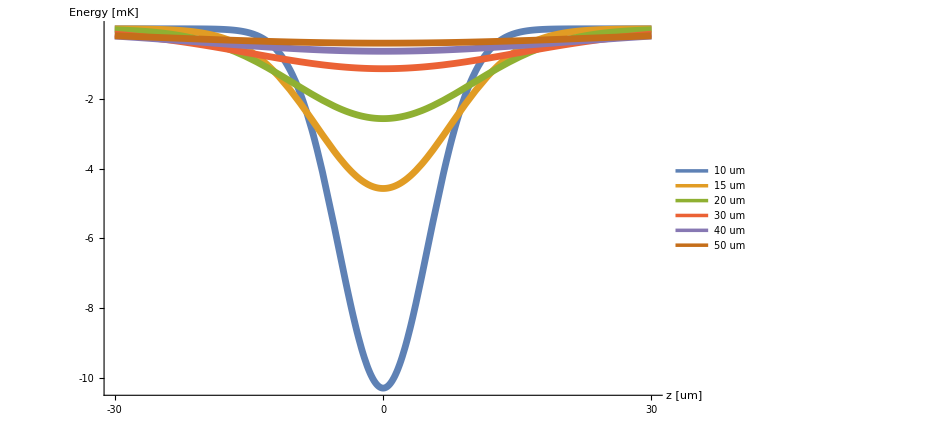

```mathematica
αUX1Σ1[x_,y_,z_]=(10^3 COmass/k)αPotential[αX1Σ1,ElFieldIPG[x,y,z]];   (* X^1 Subscript[Σ, 1] ground state polarizability potential expressed in [mK] *)
zsections= Table[αUX1Σ1[0,0,z][[1,iw]],{iw,1,Length[wzeroIPG]}];
zrange={z,zIPG-30,zIPG+30};
zlabels={Style["z [um]",Black,Italic,30],Style["Energy [mK]",Black,Italic,30]};
th=Thickness[0.007];
ims=700;
legends={Style["10 um",Black,Italic,30],Style["15 um",Black,Italic,30],Style["20 um",Black,Italic,30],Style["30 um",Black,Italic,30],Style["40 um",Black,Italic,30],Style["50 um",Black,Italic,30]};
ticks={{-30,0,30},{-2,-4,-6,-8,-10}};
ts=Directive[Black,30];
p1=Plot[zsections,zrange,AxesLabel->zlabels,PlotStyle->th, PlotRange->All,Evaluated->True,ImageSize->ims,PlotLegends->legends,Ticks->ticks,TicksStyle->ts]
```

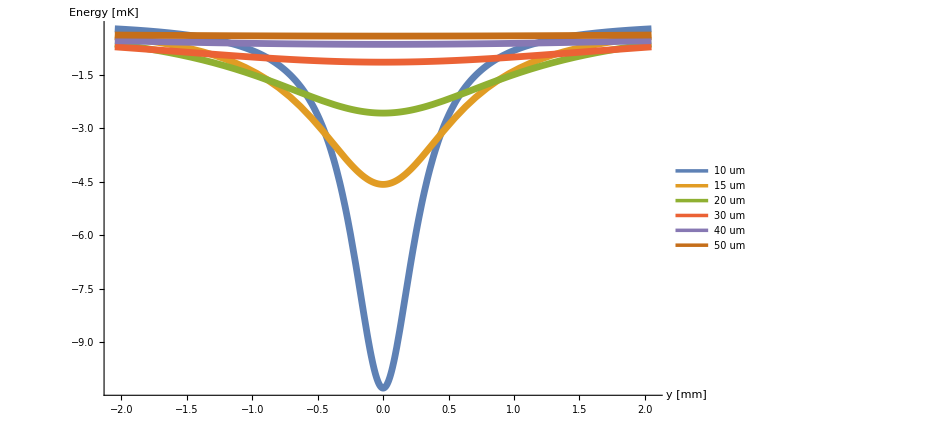

```mathematica
ysections= Table[αUX1Σ1[0,y*10^3,0][[1,iw]],{iw,1,Length[wzeroIPG]}];
yrange={y,-2.05,2.05};
ylabels={Style["y [mm]",Black,Italic,30],Style["Energy [mK]",Black,Italic,30]};
p2=Plot[ysections,yrange,AxesLabel->ylabels,PlotStyle->th, PlotRange->All,Evaluated->True,ImageSize->ims,PlotLegends->legends,TicksStyle->ts]
```

IPG trapping force field
We plot trapping force  field for different IPG waist.

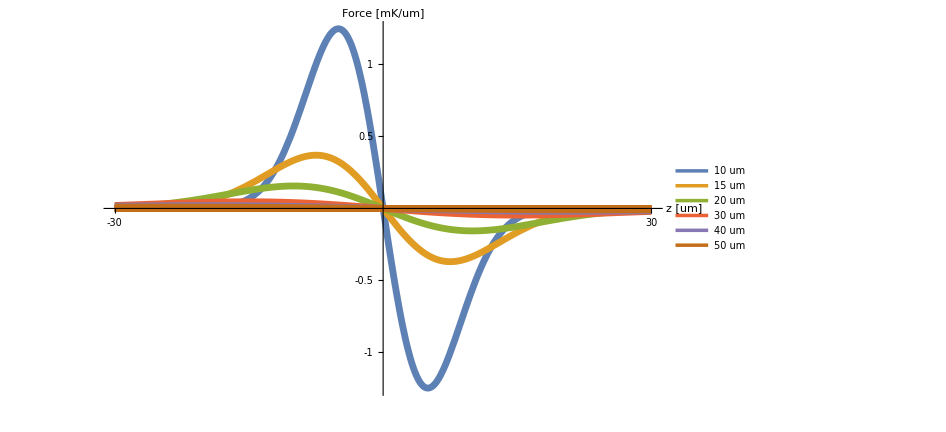

```mathematica
ForceαUX1Σ1[x_,y_,z_]=-Grad[αUX1Σ1[x,y,z],{x,y,z}];    (* Force field on X^1 Subscript[Σ, 1] ground state due to polarizability potential *)
zForce=Table[ForceαUX1Σ1[0,0,z][[1,iw]],{iw,1,Length[wzeroIPG]}];
zlabelforce={Style["z [um]",Black,Italic,30],Style["Force [mK/um]",Black,Italic,30]};
ticksforce={{-30,30},{1,0.5,-1,-0.5}};
p3=Plot[zForce,zrange,AxesLabel->zlabelforce,PlotStyle->th, PlotRange->All,Evaluated->True,ImageSize->ims,PlotLegends->legends,Ticks->ticksforce,TicksStyle->ts]
```

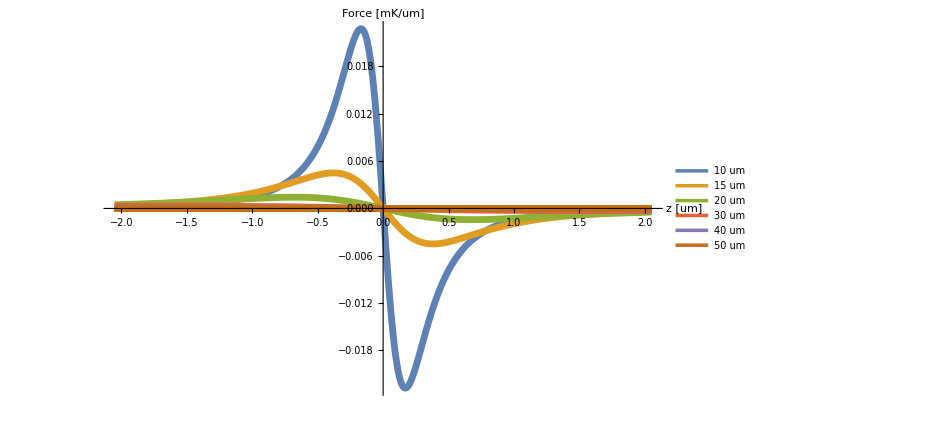

```mathematica
yForce=Table[ForceαUX1Σ1[0,y*10^3,0][[1,iw]],{iw,1,Length[wzeroIPG]}];
zlabelforce={Style["z [um]",Black,Italic,30],Style["Force [mK/um]",Black,Italic,30]};
ticksforce={{-30,30},{1,0.5,-1,-0.5}};
p3=Plot[yForce,yrange,AxesLabel->zlabelforce,PlotStyle->th, PlotRange->All,Evaluated->True,ImageSize->ims,PlotLegends->legends,TicksStyle->ts]
```

Constraints on electric field gradient
Graphical representation of constraints invloving the electric field gradient, the trap waist and the microtrap's longitudinal speed and temperature.

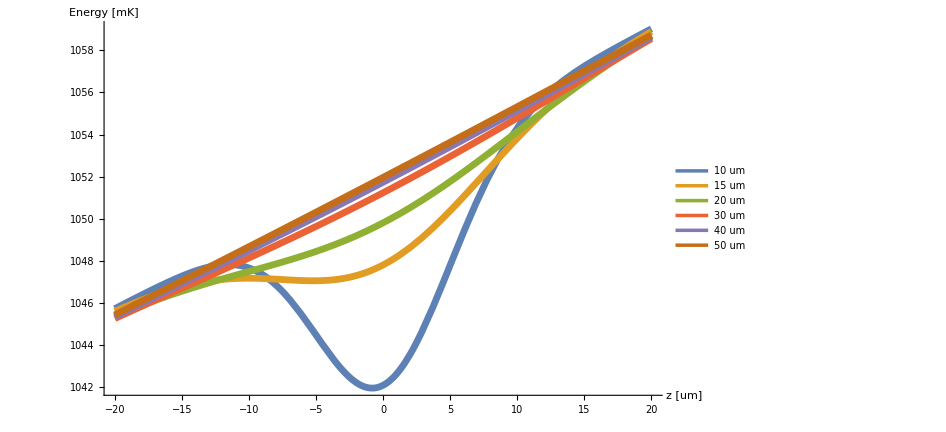

```mathematica
μUa3Π1[El_]=μPotential[μa3Π1,Λa3Π1,El] ;       (* a^3 Subscript[Π, 1] DC Stark potential divided for CO mass *)
ElStop[v_]=√(((v^2/2+Λa3Π1)^2-Λa3Π1^2)/μa3Π1^2);   (* find electric field values to stop a^3 Subscript[Π, 1] molecules with different speed by DC Stark potential *)
vel=25;
GradE=2 10^-3;  (* a feasible value of electric field gradient [V/um^2] *)
ElB[z_]=ElStop[vel]+GradE*z;
Ua3Π1[x_,y_,z_]=10^3 COmass/k(μPotential[μa3Π1,Λa3Π1,ElB[z]]+αPotential[αa3Π1,ElFieldIPG[x,y,z]] );      (* Physical potential for a^3 Subscript[Π, 1] expressed in [mK] *)
zsectionUex=Table[Ua3Π1[0,0,z][[1,iw]],{iw,1,Length[wzeroIPG]}];
size=25;
zlabelU={Style["z [um]",Black,Italic,size],Style["Energy [mK]",Black,Italic,size]};
Plot[zsectionUex,{z,zIPG-20,zIPG+20},AxesLabel->zlabelU,PlotStyle->th, PlotRange->All,Evaluated->True,ImageSize->ims,PlotLegends->legends,Ticks->{Automatic},TicksStyle->ts]
```

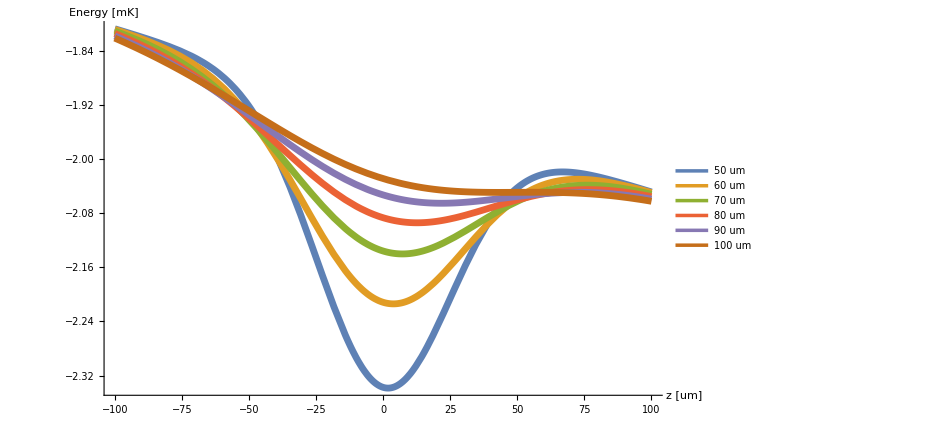

```mathematica
wIPG1={50,60,70,80,90,100}  ;       (* IPG waist expressed in um *) 
ElFieldIPG1[x_,y_,z_]=Table[AbsEl[x,y,z,powerIPG[[ip]],wIPG1[[iw]],λIPG,xIPG,yIPG,zIPG],{ip,1,1},{iw,1,Length[wIPG1]}];  
UX1Σ1[x_,y_,z_]=10^3 COmass/k(gsPotential[gsConstant,ElB[z]]+αPotential[αX1Σ1,ElFieldIPG1[x,y,z]]);       (* Physical potential for X^1 Subscript[Σ, 1] divided for CO mass *)
zsectionUgs=Table[UX1Σ1[0,0,z][[1,iw]],{iw,1,Length[wzeroIPG]}];
nlegends={Style["50 um",Black,Italic,size],Style["60 um",Black,Italic,size],Style["70 um",Black,Italic,size],Style["80 um",Black,Italic,size],Style["90 um",Black,Italic,size],Style["100 um",Black,Italic,size]};
Plot[zsectionUgs,{z,zIPG-100,zIPG+100},AxesLabel->zlabelU,PlotStyle->th, PlotRange->All,Evaluated->True,ImageSize->ims,PlotLegends->nlegends,Ticks->{Automatic},TicksStyle->ts]
```

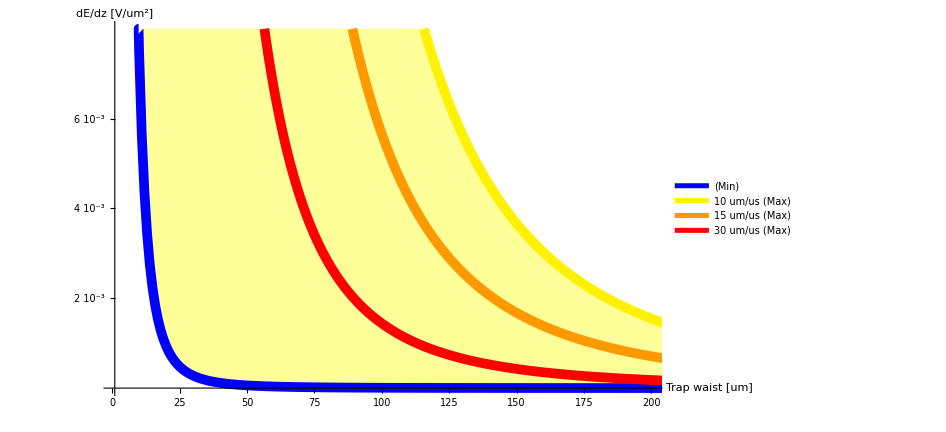
Null -Graphics-

```mathematica
ManyIPG=Array[5+ #*1&,203]  ;       (* IPG waist [um] *) 
ElIPG[x_,y_,z_]=Table[AbsEl[x,y,z,powerIPG[[ip]],ManyIPG[[iw]],λIPG,xIPG,yIPG,zIPG],{ip,1,1},{iw,1,Length[ManyIPG]}];  
UX1Σ1[x_,y_,z_]=(10^3 COmass/k)αPotential[αX1Σ1,ElIPG[x,y,z]];   (* X^1 Subscript[Σ, 1] ground state polarizability potential expressed in [mK] *)
ForceUX1Σ1[x_,y_,z_]=-Grad[UX1Σ1[x,y,z],{x,y,z}];    (* Force field on X^1 Subscript[Σ, 1] ground state due to polarizability potential *)
ManyMaxForceZ=Table[MaxValue[ForceUX1Σ1[0,0,z][[1,i,3]],z],{i,1,Length[ManyIPG]}]; (* max z-force [mK/um] for different IPG waist*)
ManyProductEgradzE=(10^-3 k)/(2gsConstant COmass)ManyMaxForceZ ;
vchip={10,15,30};
MaxGradzE=Table[ManyProductEgradzE/(ElStop[vchip][[i]]),{i,1,Length[vchip]}];
MinGradzE=Table[(10^-3 k ManyMaxForceZ √(μa3Π1^2(ElStop[vchip][[i]])^2+Λa3Π1^2))/(μa3Π1^2 ElStop[vchip][[i]]COmass),{i,1,Length[vchip]}];
MaxGrad=Table[Transpose@{ManyIPG,MaxGradzE[[i]]},{i,1,Length[vchip]}];
MinGrad= Table[Transpose@{ManyIPG,MinGradzE[[i]]},{i,1,Length[vchip]}];
tickSpec=Table[{2i 10^-3,2i Superscript[10,-3]},{i,1,3}];

Show[ListLinePlot[{MinGrad[[1]],MaxGrad[[1]],MaxGrad[[2]],MaxGrad[[3]]},Filling->{1->{{2},{RGBColor[1,1,0.6],None}}},PlotStyle->{{RGBColor[0,0,1],Thickness[0.01]},{RGBColor[1,0.95,0],Thickness[0.01]},{RGBColor[1,0.6,0],Thickness[0.01]},{RGBColor[1,0,0],Thickness[0.01]}},PlotLegends-> {Style["(Min)",Black,Italic,size],Style[ vchip[[1]]"um/us (Max)",Black,Italic,size],Style[ vchip[[2]]"um/us (Max)",Black,Italic,size],Style[ vchip[[3]]"um/us (Max)",Black,Italic,size]}, PlotRange->{{1,200},{0,8 10^-3}},Ticks->{Automatic,tickSpec}, AxesLabel->{Style["Trap waist [um]",Black,Italic,size],Style["dE/dz [V/um^2]",Black,Italic,size]},ImageSize->700,TicksStyle->Directive[Black,size]],Graphics[Text[Style["Vel=10 um/us",FontSize->size,Black],{45,0.8}]]]
```

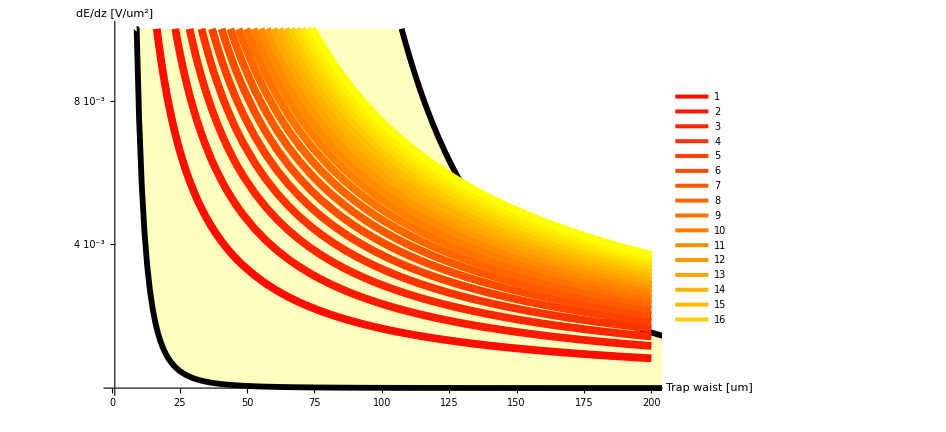

```mathematica
V=Array[0+ #&,30] ;  (* Microtrap speed [μm/μs] *) 
T=Array[0+ #&,20] ;  (* Microtrap temperature [mK] *) 
σ=√((k  T 10^-3)/COmass) ; (* sigma z speed [μm/μs] *)
DeltaEl=Table[ElStop[V[[iV]]+σ[[iT]]]-ElStop[V[[iV]]-σ[[iT]]],{iV,1,Length[V]},{iT,1,Length[T]}];

size=30;
col=Table[RGBColor[1,g,0],{g,0.05,1,0.05}];
tickSpecification=Table[{4i 10^-3,4i Superscript[10,-3]},{i,1,2}];
FirstThickness=0.006;
SecondThickness=0.008;
num=15;

curves=DeltaEl[[num,All]]/(2 x);
colorf=Blend[{{0,Red},{20,Yellow}},Round[#,0.1]]& ;
BarLegend[{colorf[#]&,{1,20}},LabelStyle->{Black,FontSize->30}]

Show[ListLinePlot[{MinGrad[[1]],MaxGrad[[1]]},Filling->{1->{{2},{RGBColor[1,1,0.75],None}}},PlotStyle->{{Black,Thickness[FirstThickness]},{Black,Thickness[FirstThickness]}}, PlotRange->{{1,200},{0,10 10^-3}},Ticks->{Automatic,tickSpecification}, AxesLabel->{Style["Trap waist [um]",Black,Italic,size],Style["dE/dz [V/um^2]",Black,Italic,size]},ImageSize->700,TicksStyle->Directive[Black,size]],Plot[curves,{x,0,200},PlotRange->{{1,200},{0,10 10^-3}},PlotStyle->Table[{col[[i]],Thickness[SecondThickness]},{i,1,Length[col]}],PlotLegends-> Table[Style[ToString[T[[iT]]],Black,Italic,size],{iT,1,Length[T]}]]]
```

Non-adiabatic transitions
Estimate the values of adiabatic parameters, in order to check the consistency of adiabatic approximation during the Stark decelation phenomenon.

```mathematica
ℏ=1.055 10^-34;(* [Js] *)
Λ=394 10^6 ℏ 2π; (* [J] *)
μ=1.37*3.335 10^-30;  (* [Cm] -> μE/2 is expressed in [J] *)
MicrotrapVel=Array[ #&,20];
ElStop[v_]=√(((v^2/2+Λa3Π1)^2-Λa3Π1^2)/μa3Π1^2); 
ElGrad=Array[ #*10^-3 10^12&,10];  (* [V/m^2] *)
a=ConstantArray[0,{Length@MicrotrapVel,Length@ElGrad}];
For[iV=1,iV≤ Length@MicrotrapVel,iV++,
For[iG=1,iG≤ Length@ElGrad,iG++,H={{Λ/2,(μ ElStop[MicrotrapVel[[iV]]])/2},{(μ ElStop[MicrotrapVel[[iV]]])/2,-Λ/2}};ΔHΔt={{0,μ/2 ElGrad[[iG]] MicrotrapVel[[iV]]},{μ/2 ElGrad[[iG]] MicrotrapVel[[iV]],0}} ;{Energies,vects}=Eigensystem[H,Cubics->True];Eigenvec1=Normalize[vects[[1]]];
Eigenvec2=Normalize[vects[[2]]];ΔE=Energies[[2]]-Energies[[1]];a[[iV,iG]]=ℏ (Eigenvec1.ΔHΔt.Eigenvec2)/ΔE^2]];
zmesh=Array[ #*0.0001&,30] ;
tickGrad=Table[{4i ,4i Superscript[10,-3]},{i,1,2}];
ticka=Table[{3i 10^-4 ,3i Superscript[10,-4]},{i,1,2}];
ListPlot3D[a,ImageSize->700,PlotRange->All,MeshFunctions->{#3&},Mesh->{zmesh},MeshStyle->{Directive[White,Thick]},PlotStyle->{Red},Ticks->{tickGrad,Table[{j*5,MicrotrapVel[[j*5]]},{j,1,Length[MicrotrapVel]/5}],ticka},Boxed->False,AxesLabel->{Style["dE/dz [V/um^2] ",Black,Italic,25],Style["Vel [um/us] ",Black,Italic,25],Style["Adiabatic\n parameter",Black,Italic,25]},TicksStyle->Directive[Black,20]]
```

-Graphics3D-